```mathematica
c = {(1-t)^2,2t(1-t),t^2}
```

{(1-t)^2,2 (1-t) t,t^2}

```mathematica
P = {{P0x,P0y},{P1x,P1y},{P2x,P2y}}
PA = {{P0xA,P0yA},{P1xA,P1yA},{P2xA,P2yA}}
PB = {{P0xB,P0yB},{P1xB,P1yB},{P2xB,P2yB}}
```

{{P0x,P0y},{P1x,P1y},{P2x,P2y}}

{{P0xA,P0yA},{P1xA,P1yA},{P2xA,P2yA}}

{{P0xB,P0yB},{P1xB,P1yB},{P2xB,P2yB}}

```mathematica
d0=(c.(P)).(c.(P))
```

(P0x (1-t)^2+2 P1x (1-t) t+P2x t^2)^2+(P0y (1-t)^2+2 P1y (1-t) t+P2y t^2)^2

```mathematica
dl=Sqrt[(D[((c.(P))[[1]]),t])^2+(D[((c.(P))[[2]]),t])^2]
```

√((-2 P0x (1-t)+2 P1x (1-t)-2 P1x t+2 P2x t)^2+(-2 P0y (1-t)+2 P1y (1-t)-2 P1y t+2 P2y t)^2)

```mathematica
Integrate[dl^2,{t,0,1}]
```

```mathematica
int2=4/3 (P0x^2+P0y^2+P1x^2+P1y^2-P1x P2x+P2x^2-P0x (P1x+P2x)-P1y P2y+P2y^2-P0y (P1y+P2y))
```

4/3 (P0x^2+P0y^2+P1x^2+P1y^2-P1x P2x+P2x^2-P0x (P1x+P2x)-P1y P2y+P2y^2-P0y (P1y+P2y))

```mathematica
int2//Simplify
```

4/3 (P0x^2+P0y^2+P1x^2+P1y^2-P1x P2x+P2x^2-P0x (P1x+P2x)-P1y P2y+P2y^2-P0y (P1y+P2y))

```mathematica
pvec = {P0x,P1x,P2x, P0y,P1y,P2y}
```

{P0x,P1x,P2x,P0y,P1y,P2y}

```mathematica
l2coeffArray=CoefficientArrays[4/3 (P0x^2+P0y^2+P1x^2+P1y^2-P1x P2x+P2x^2-P0x (P1x+P2x)-P1y P2y+P2y^2-P0y (P1y+P2y)),pvec]
```

{0,SparseArray[<0>, {6}],SparseArray[<12>, {6, 6}]}

```mathematica
m=l2coeffArray[[3]]
```

SparseArray[<12>, {6, 6}]

```mathematica
w=1/2(m+Transpose[m])
```

SparseArray[<18>, {6, 6}]

```mathematica
m
```

SparseArray[<12>, {6, 6}]

```mathematica
m//MatrixForm
```

(4/3 | -4/3 | -4/3 | 0 | 0 | 0
0 | 4/3 | -4/3 | 0 | 0 | 0
0 | 0 | 4/3 | 0 | 0 | 0
0 | 0 | 0 | 4/3 | -4/3 | -4/3
0 | 0 | 0 | 0 | 4/3 | -4/3
0 | 0 | 0 | 0 | 0 | 4/3)

```mathematica
w/(2/3)//MatrixForm
```

(2 | -1 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0
-1 | -1 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | -1 | -1
0 | 0 | 0 | -1 | 2 | -1
0 | 0 | 0 | -1 | -1 | 2)

```mathematica
arcLength2=pvec.w.pvec
```

P0x ((4 P0x)/3-(2 P1x)/3-(2 P2x)/3)+P1x (-(2 P0x)/3+(4 P1x)/3-(2 P2x)/3)+P2x (-(2 P0x)/3-(2 P1x)/3+(4 P2x)/3)+P0y ((4 P0y)/3-(2 P1y)/3-(2 P2y)/3)+P1y (-(2 P0y)/3+(4 P1y)/3-(2 P2y)/3)+P2y (-(2 P0y)/3-(2 P1y)/3+(4 P2y)/3)

```mathematica
Minimize[arcLength2,{P1x,P1y}]//FullSimplify
Maximize[arcLength2,{P1x,P1y}]//FullSimplify
```

{(P0x-P2x)^2+(P0y-P2y)^2,{P1x→(P0x+P2x)/2,P1y→(P0y+P2y)/2}}

{∞,{P1x→Indeterminate,P1y→Indeterminate}}

```mathematica
pavec=Flatten[Transpose[PA]]
pbvec=Flatten[Transpose[PB]]
pdiffvec=Flatten[Transpose[PA-PB]]
```

{P0xA,P1xA,P2xA,P0yA,P1yA,P2yA}

{P0xB,P1xB,P2xB,P0yB,P1yB,P2yB}

{P0xA-P0xB,P1xA-P1xB,P2xA-P2xB,P0yA-P0yB,P1yA-P1yB,P2yA-P2yB}

```mathematica
aLength = pavec.w.pavec
bLength = pbvec.w.pbvec
d=(c.(PA-PB)).(c.(PA-PB))

total=aLength+bLength-d
```

P0xA ((4 P0xA)/3-(2 P1xA)/3-(2 P2xA)/3)+P1xA (-(2 P0xA)/3+(4 P1xA)/3-(2 P2xA)/3)+P2xA (-(2 P0xA)/3-(2 P1xA)/3+(4 P2xA)/3)+P0yA ((4 P0yA)/3-(2 P1yA)/3-(2 P2yA)/3)+P1yA (-(2 P0yA)/3+(4 P1yA)/3-(2 P2yA)/3)+P2yA (-(2 P0yA)/3-(2 P1yA)/3+(4 P2yA)/3)

P0xB ((4 P0xB)/3-(2 P1xB)/3-(2 P2xB)/3)+P1xB (-(2 P0xB)/3+(4 P1xB)/3-(2 P2xB)/3)+P2xB (-(2 P0xB)/3-(2 P1xB)/3+(4 P2xB)/3)+P0yB ((4 P0yB)/3-(2 P1yB)/3-(2 P2yB)/3)+P1yB (-(2 P0yB)/3+(4 P1yB)/3-(2 P2yB)/3)+P2yB (-(2 P0yB)/3-(2 P1yB)/3+(4 P2yB)/3)

((P0xA-P0xB) (1-t)^2+2 (P1xA-P1xB) (1-t) t+(P2xA-P2xB) t^2)^2+((P0yA-P0yB) (1-t)^2+2 (P1yA-P1yB) (1-t) t+(P2yA-P2yB) t^2)^2

P0xA ((4 P0xA)/3-(2 P1xA)/3-(2 P2xA)/3)+P1xA (-(2 P0xA)/3+(4 P1xA)/3-(2 P2xA)/3)+P2xA (-(2 P0xA)/3-(2 P1xA)/3+(4 P2xA)/3)+P0xB ((4 P0xB)/3-(2 P1xB)/3-(2 P2xB)/3)+P1xB (-(2 P0xB)/3+(4 P1xB)/3-(2 P2xB)/3)+P2xB (-(2 P0xB)/3-(2 P1xB)/3+(4 P2xB)/3)+P0yA ((4 P0yA)/3-(2 P1yA)/3-(2 P2yA)/3)+P1yA (-(2 P0yA)/3+(4 P1yA)/3-(2 P2yA)/3)+P2yA (-(2 P0yA)/3-(2 P1yA)/3+(4 P2yA)/3)+P0yB ((4 P0yB)/3-(2 P1yB)/3-(2 P2yB)/3)+P1yB (-(2 P0yB)/3+(4 P1yB)/3-(2 P2yB)/3)+P2yB (-(2 P0yB)/3-(2 P1yB)/3+(4 P2yB)/3)-((P0xA-P0xB) (1-t)^2+2 (P1xA-P1xB) (1-t) t+(P2xA-P2xB) t^2)^2-((P0yA-P0yB) (1-t)^2+2 (P1yA-P1yB) (1-t) t+(P2yA-P2yB) t^2)^2

{P0xA,P0yA,P0xB,P0yB}

```mathematica
pcombinedvec=({pavec,pbvec}//Flatten)
pinterestvec = {PA[[2]],PB[[2]]}//Flatten
```

{P0xA,P1xA,P2xA,P0yA,P1yA,P2yA,P0xB,P1xB,P2xB,P0yB,P1yB,P2yB}

{P1xA,P1yA,P1xB,P1yB}

```mathematica
coeffMatrix=CoefficientArrays[total,pinterestvec]
```

{(4 P0xA^2)/3+(4 P0xB^2)/3+(4 P0yA^2)/3+(4 P0yB^2)/3-(4 P0xA P2xA)/3+(4 P2xA^2)/3-(4 P0xB P2xB)/3+(4 P2xB^2)/3-(4 P0yA P2yA)/3+(4 P2yA^2)/3-(4 P0yB P2yB)/3+(4 P2yB^2)/3-(P0xA-P0xB)^2 (1-t)^4-(P0yA-P0yB)^2 (1-t)^4-2 (P0xA-P0xB) (P2xA-P2xB) (1-t)^2 t^2-2 (P0yA-P0yB) (P2yA-P2yB) (1-t)^2 t^2-(P2xA-P2xB)^2 t^4-(P2yA-P2yB)^2 t^4,SparseArray[<4>, {4}],SparseArray[<6>, {4, 4}]}

```mathematica
pint=(-1/2)Inverse[coeffMatrix[[3]]].coeffMatrix[[2]]//Simplify
```

{1/(2 (1-3 t^2+6 t^3-3 t^4)^2)(P2xA (1-3 t^2+9 t^3-6 t^4+9 t^5-27 t^6+27 t^7-9 t^8)+P0xA (1+3 t-12 t^2+24 t^3-51 t^4+90 t^5-90 t^6+45 t^7-9 t^8)+3 (-1+t) t (P2xB t (2-t+3 t^3-6 t^4+3 t^5)+P0xB (1+2 t^2-12 t^3+18 t^4-12 t^5+3 t^6))),1/(2 (1-3 t^2+6 t^3-3 t^4)^2)(P2yA (1-3 t^2+9 t^3-6 t^4+9 t^5-27 t^6+27 t^7-9 t^8)+P0yA (1+3 t-12 t^2+24 t^3-51 t^4+90 t^5-90 t^6+45 t^7-9 t^8)+3 (-1+t) t (P2yB t (2-t+3 t^3-6 t^4+3 t^5)+P0yB (1+2 t^2-12 t^3+18 t^4-12 t^5+3 t^6))),-(-(4 P0xB)/3-(4 P2xB)/3-4 (P0xA-P0xB) (-1+t)^3 t-4 (P2xA-P2xB) (-1+t) t^3)/(2 (4/3-4 (-1+t)^2 t^2)),-(-(4 P0yB)/3-(4 P2yB)/3-4 (P0yA-P0yB) (-1+t)^3 t-4 (P2yA-P2yB) (-1+t) t^3)/(2 (4/3-4 (-1+t)^2 t^2))}

```mathematica
pint[[1]]
```

1/(2 (1-3 t^2+6 t^3-3 t^4)^2)(P2xA (1-3 t^2+9 t^3-6 t^4+9 t^5-27 t^6+27 t^7-9 t^8)+P0xA (1+3 t-12 t^2+24 t^3-51 t^4+90 t^5-90 t^6+45 t^7-9 t^8)+3 (-1+t) t (P2xB t (2-t+3 t^3-6 t^4+3 t^5)+P0xB (1+2 t^2-12 t^3+18 t^4-12 t^5+3 t^6)))

```mathematica
prules=Table[(pinterestvec[[i]])-> (pint[[i]]),{i,1,4}]
```

{P1xA→1/(2 (1-3 t^2+6 t^3-3 t^4)^2)(P2xA (1-3 t^2+9 t^3-6 t^4+9 t^5-27 t^6+27 t^7-9 t^8)+P0xA (1+3 t-12 t^2+24 t^3-51 t^4+90 t^5-90 t^6+45 t^7-9 t^8)+3 (-1+t) t (P2xB t (2-t+3 t^3-6 t^4+3 t^5)+P0xB (1+2 t^2-12 t^3+18 t^4-12 t^5+3 t^6))),P1yA→1/(2 (1-3 t^2+6 t^3-3 t^4)^2)(P2yA (1-3 t^2+9 t^3-6 t^4+9 t^5-27 t^6+27 t^7-9 t^8)+P0yA (1+3 t-12 t^2+24 t^3-51 t^4+90 t^5-90 t^6+45 t^7-9 t^8)+3 (-1+t) t (P2yB t (2-t+3 t^3-6 t^4+3 t^5)+P0yB (1+2 t^2-12 t^3+18 t^4-12 t^5+3 t^6))),P1xB→-(-(4 P0xB)/3-(4 P2xB)/3-4 (P0xA-P0xB) (-1+t)^3 t-4 (P2xA-P2xB) (-1+t) t^3)/(2 (4/3-4 (-1+t)^2 t^2)),P1yB→-(-(4 P0yB)/3-(4 P2yB)/3-4 (P0yA-P0yB) (-1+t)^3 t-4 (P2yA-P2yB) (-1+t) t^3)/(2 (4/3-4 (-1+t)^2 t^2))}

```mathematica
dopt=d/.prules//Simplify
```

1/((1-3 t^2+6 t^3-3 t^4)^4)((P2xA t (-1+3 t^2-9 t^3+9 t^4-12 t^5+36 t^6-54 t^7+36 t^8-9 t^9)+P2xB t (1+3 t^2-9 t^3+9 t^4+6 t^5-36 t^6+54 t^7-36 t^8+9 t^9)+P0xA (-1+t+3 t^3-18 t^4+63 t^5-138 t^6+180 t^7-135 t^8+54 t^9-9 t^10)+P0xB (1-t+3 t^3-45 t^5+132 t^6-180 t^7+135 t^8-54 t^9+9 t^10))^2+(P2yA t (-1+3 t^2-9 t^3+9 t^4-12 t^5+36 t^6-54 t^7+36 t^8-9 t^9)+P2yB t (1+3 t^2-9 t^3+9 t^4+6 t^5-36 t^6+54 t^7-36 t^8+9 t^9)+P0yA (-1+t+3 t^3-18 t^4+63 t^5-138 t^6+180 t^7-135 t^8+54 t^9-9 t^10)+P0yB (1-t+3 t^3-45 t^5+132 t^6-180 t^7+135 t^8-54 t^9+9 t^10))^2)

```mathematica
Minimize[dopt,t]
```

$Aborted

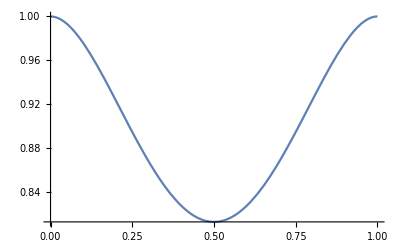

```mathematica
Plot[1-3 t^2+6 t^3-3 t^4,{t,0,1}]
```

```mathematica
Assuming[0<t<1,Simplify[D[dopt,t]==0]]
```

```mathematica
Collect[(24 t (1-3 t+2 t^2) ((P2xA t (-1+3 t^2-9 t^3+9 t^4-12 t^5+36 t^6-54 t^7+36 t^8-9 t^9)+P2xB t (1+3 t^2-9 t^3+9 t^4+6 t^5-36 t^6+54 t^7-36 t^8+9 t^9)+P0xA (-1+t+3 t^3-18 t^4+63 t^5-138 t^6+180 t^7-135 t^8+54 t^9-9 t^10)+P0xB (1-t+3 t^3-45 t^5+132 t^6-180 t^7+135 t^8-54 t^9+9 t^10))^2+(P2yA t (-1+3 t^2-9 t^3+9 t^4-12 t^5+36 t^6-54 t^7+36 t^8-9 t^9)+P2yB t (1+3 t^2-9 t^3+9 t^4+6 t^5-36 t^6+54 t^7-36 t^8+9 t^9)+P0yA (-1+t+3 t^3-18 t^4+63 t^5-138 t^6+180 t^7-135 t^8+54 t^9-9 t^10)+P0yB (1-t+3 t^3-45 t^5+132 t^6-180 t^7+135 t^8-54 t^9+9 t^10))^2)+(1-3 t^2+6 t^3-3 t^4) (2 (P2xA-P2xB-9 P2xA t^2-9 P2xB t^2+36 P2xA t^3+36 P2xB t^3-45 P2xA t^4-45 P2xB t^4+72 P2xA t^5-36 P2xB t^5-252 P2xA t^6+252 P2xB t^6+432 P2xA t^7-432 P2xB t^7-324 P2xA t^8+324 P2xB t^8+90 P2xA t^9-90 P2xB t^9+P0xB (1-9 t^2+225 t^4-792 t^5+1260 t^6-1080 t^7+486 t^8-90 t^9)+P0xA (-1-9 t^2+72 t^3-315 t^4+828 t^5-1260 t^6+1080 t^7-486 t^8+90 t^9)) (-P2xB t (1+3 t^2-9 t^3+9 t^4+6 t^5-36 t^6+54 t^7-36 t^8+9 t^9)+P2xA t (1-3 t^2+9 t^3-9 t^4+12 t^5-36 t^6+54 t^7-36 t^8+9 t^9)+P0xB (-1+t-3 t^3+45 t^5-132 t^6+180 t^7-135 t^8+54 t^9-9 t^10)+P0xA (1-t-3 t^3+18 t^4-63 t^5+138 t^6-180 t^7+135 t^8-54 t^9+9 t^10))+2 (P2yA-P2yB-9 P2yA t^2-9 P2yB t^2+36 P2yA t^3+36 P2yB t^3-45 P2yA t^4-45 P2yB t^4+72 P2yA t^5-36 P2yB t^5-252 P2yA t^6+252 P2yB t^6+432 P2yA t^7-432 P2yB t^7-324 P2yA t^8+324 P2yB t^8+90 P2yA t^9-90 P2yB t^9+P0yB (1-9 t^2+225 t^4-792 t^5+1260 t^6-1080 t^7+486 t^8-90 t^9)+P0yA (-1-9 t^2+72 t^3-315 t^4+828 t^5-1260 t^6+1080 t^7-486 t^8+90 t^9)) (-P2yB t (1+3 t^2-9 t^3+9 t^4+6 t^5-36 t^6+54 t^7-36 t^8+9 t^9)+P2yA t (1-3 t^2+9 t^3-9 t^4+12 t^5-36 t^6+54 t^7-36 t^8+9 t^9)+P0yB (-1+t-3 t^3+45 t^5-132 t^6+180 t^7-135 t^8+54 t^9-9 t^10)+P0yA (1-t-3 t^3+18 t^4-63 t^5+138 t^6-180 t^7+135 t^8-54 t^9+9 t^10))))==0,t]
```

```mathematica
-2 P0xA^2+4 P0xA P0xB-2 P0xB^2-2 P0yA^2+4 P0yA P0yB-2 P0yB^2+2 P0xA P2xA-2 P0xB P2xA-2 P0xA P2xB+2 P0xB P2xB+2 P0yA P2yA-2 P0yB P2yA-2 P0yA P2yB+2 P0yB P2yB+(26 P0xA^2-52 P0xA P0xB+26 P0xB^2+26 P0yA^2-52 P0yA P0yB+26 P0yB^2-4 P0xA P2xA+4 P0xB P2xA+2 P2xA^2+4 P0xA P2xB-4 P0xB P2xB-4 P2xA P2xB+2 P2xB^2-4 P0yA P2yA+4 P0yB P2yA+2 P2yA^2+4 P0yA P2yB-4 P0yB P2yB-4 P2yA P2yB+2 P2yB^2) t+(-132 P0xA^2+228 P0xA P0xB-96 P0xB^2-132 P0yA^2+228 P0yA P0yB-96 P0yB^2+24 P0xA P2xA-24 P0xB P2xA-60 P0xA P2xB+60 P0xB P2xB+24 P0yA P2yA-24 P0yB P2yA-60 P0yA P2yB+60 P0yB P2yB) t^2+(366 P0xA^2-540 P0xA P0xB+174 P0xB^2+366 P0yA^2-540 P0yA P0yB+174 P0yB^2-96 P0xA P2xA+48 P0xB P2xA-6 P2xA^2+288 P0xA P2xB-240 P0xB P2xB-36 P2xA P2xB+42 P2xB^2-96 P0yA P2yA+48 P0yB P2yA-6 P2yA^2+288 P0yA P2yB-240 P0yB P2yB-36 P2yA P2yB+42 P2yB^2) t^3+(-1050 P0xA^2+1560 P0xA P0xB-510 P0xB^2-1050 P0yA^2+1560 P0yA P0yB-510 P0yB^2+120 P0xA P2xA+60 P0xB P2xA+30 P2xA^2-660 P0xA P2xB+480 P0xB P2xB+120 P2xA P2xB-150 P2xB^2+120 P0yA P2yA+60 P0yB P2yA+30 P2yA^2-660 P0yA P2yB+480 P0yB P2yB+120 P2yA P2yB-150 P2yB^2) t^4+(3336 P0xA^2-4944 P0xA P0xB+1824 P0xB^2+3336 P0yA^2-4944 P0yA P0yB+1824 P0yB^2+60 P0xA P2xA-204 P0xB P2xA-84 P2xA^2+1668 P0xA P2xB-1092 P0xB P2xB+24 P2xA P2xB+276 P2xB^2+60 P0yA P2yA-204 P0yB P2yA-84 P2yA^2+1668 P0yA P2yB-1092 P0yB P2yB+24 P2yA P2yB+276 P2yB^2) t^5+(-8916 P0xA^2+12060 P0xA P0xB-4656 P0xB^2-8916 P0yA^2+12060 P0yA P0yB-4656 P0yB^2-972 P0xA P2xA+444 P0xB P2xA+240 P2xA^2-4800 P0xA P2xB+2304 P0xB P2xB-1008 P2xA P2xB-744 P2xB^2-972 P0yA P2yA+444 P0yB P2yA+240 P2yA^2-4800 P0yA P2yB+2304 P0yB P2yB-1008 P2yA P2yB-744 P2yB^2) t^6+(21438 P0xA^2-25524 P0xA P0xB+8622 P0xB^2+21438 P0yA^2-25524 P0yA P0yB+8622 P0yB^2+4860 P0xA P2xA-2484 P0xB P2xA-522 P2xA^2+12492 P0xA P2xB-5796 P0xB P2xB+3420 P2xA P2xB+1638 P2xB^2+4860 P0yA P2yA-2484 P0yB P2yA-522 P2yA^2+12492 P0yA P2yB-5796 P0yB P2yB+3420 P2yA P2yB+1638 P2yB^2) t^7+(-53640 P0xA^2+59400 P0xA P0xB-14184 P0xB^2-53640 P0yA^2+59400 P0yA P0yB-14184 P0yB^2-17982 P0xA P2xA+11106 P0xB P2xA-306 P2xA^2-29898 P0xA P2xB+19926 P0xB P2xB-6264 P2xA P2xB-1854 P2xB^2-17982 P0yA P2yA+11106 P0yB P2yA-306 P2yA^2-29898 P0yA P2yB+19926 P0yB P2yB-6264 P2yA P2yB-1854 P2yB^2) t^8+(136080 P0xA^2-163440 P0xA P0xB+40320 P0xB^2+136080 P0yA^2-163440 P0yA P0yB+40320 P0yB^2+50760 P0xA P2xA-31680 P0xB P2xA+5040 P2xA^2+57960 P0xA P2xB-51120 P0xB P2xB+9000 P2xA P2xB-1080 P2xB^2+50760 P0yA P2yA-31680 P0yB P2yA+5040 P2yA^2+57960 P0yA P2yB-51120 P0yB P2yB+9000 P2yA P2yB-1080 P2yB^2) t^9+(-313290 P0xA^2+442980 P0xA P0xB-148698 P0xB^2-313290 P0yA^2+442980 P0yA P0yB-148698 P0yB^2-112860 P0xA P2xA+69552 P0xB P2xA-14814 P2xA^2-70740 P0xA P2xB+76032 P0xB P2xB-13680 P2xA P2xB+9486 P2xB^2-112860 P0yA P2yA+69552 P0yB P2yA-14814 P2yA^2-70740 P0yA P2yB+76032 P0yB P2yB-13680 P2yA P2yB+9486 P2yB^2) t^10+(596538 P0xA^2-967788 P0xA P0xB+394362 P0xB^2+596538 P0yA^2-967788 P0yA P0yB+394362 P0yB^2+214704 P0xA P2xA-148824 P0xB P2xA+24894 P2xA^2+10584 P0xA P2xB-30240 P0xB P2xB+16092 P2xA P2xB-17874 P2xB^2+214704 P0yA P2yA-148824 P0yB P2yA+24894 P2yA^2+10584 P0yA P2yB-30240 P0yB P2yB+16092 P2yA P2yB-17874 P2yB^2) t^11+(-865350 P0xA^2+1525068 P0xA P0xB-679374 P0xB^2-865350 P0yA^2+1525068 P0yA P0yB-679374 P0yB^2-360828 P0xA P2xA+301104 P0xB P2xA-30402 P2xA^2+155196 P0xA P2xB-134784 P0xB P2xB+1080 P2xA P2xB+9666 P2xB^2-360828 P0yA P2yA+301104 P0yB P2yA-30402 P2yA^2+155196 P0yA P2yB-134784 P0yB P2yB+1080 P2yA P2yB+9666 P2yB^2) t^12+(842886 P0xA^2-1539108 P0xA P0xB+706806 P0xB^2+842886 P0yA^2-1539108 P0yA P0yB+706806 P0yB^2+481248 P0xA P2xA-457056 P0xB P2xA+38826 P2xA^2-334584 P0xA P2xB+331560 P0xB P2xB-53460 P2xA P2xB+25218 P2xB^2+481248 P0yA P2yA-457056 P0yB P2yA+38826 P2yA^2-334584 P0yA P2yB+331560 P0yB P2yB-53460 P2yA P2yB+25218 P2yB^2) t^13+(-309690 P0xA^2+533520 P0xA P0xB-227070 P0xB^2-309690 P0yA^2+533520 P0yA P0yB-227070 P0yB^2-382320 P0xA P2xA+390420 P0xB P2xA-53190 P2xA^2+296460 P0xA P2xB-311040 P0xB P2xB+114480 P2xA P2xB-64530 P2xB^2-382320 P0yA P2yA+390420 P0yB P2yA-53190 P2yA^2+296460 P0yA P2yB-311040 P0yB P2yB+114480 P2yA P2yB-64530 P2yB^2) t^14+(-589032 P0xA^2+1219104 P0xA P0xB-629640 P0xB^2-589032 P0yA^2+1219104 P0yA P0yB-629640 P0yB^2-84888 P0xA P2xA+68904 P0xB P2xA+38880 P2xA^2+125928 P0xA P2xB-109080 P0xB P2xB-93744 P2xA P2xB+55296 P2xB^2-84888 P0yA P2yA+68904 P0yB P2yA+38880 P2yA^2+125928 P0yA P2yB-109080 P0yB P2yB-93744 P2yA P2yB+55296 P2yB^2) t^15+(1357722 P0xA^2-2730024 P0xA P0xB+1372302 P0xB^2+1357722 P0yA^2-2730024 P0yA P0yB+1372302 P0yB^2+757350 P0xA P2xA-748278 P0xB P2xA+44064 P2xA^2-771930 P0xA P2xB+762858 P0xB P2xB-79056 P2xA P2xB+34992 P2xB^2+757350 P0yA P2yA-748278 P0yB P2yA+44064 P2yA^2-771930 P0yA P2yB+762858 P0yB P2yB-79056 P2yA P2yB+34992 P2yB^2) t^16+(-1570104 P0xA^2+3143448 P0xA P0xB-1573344 P0xB^2-1570104 P0yA^2+3143448 P0yA P0yB-1573344 P0yB^2-1215648 P0xA P2xA+1213056 P0xB P2xA-164592 P2xA^2+1218888 P0xA P2xB-1216296 P0xB P2xB+326592 P2xA P2xB-162000 P2xB^2-1215648 P0yA P2yA+1213056 P0yB P2yA-164592 P2yA^2+1218888 P0yA P2yB-1216296 P0yB P2yB+326592 P2yA P2yB-162000 P2yB^2) t^17+(1232334 P0xA^2-2464992 P0xA P0xB+1232658 P0xB^2+1232334 P0yA^2-2464992 P0yA P0yB+1232658 P0yB^2+1188108 P0xA P2xA-1187784 P0xB P2xA+232794 P2xA^2-1188432 P0xA P2xB+1188108 P0xB P2xB-465264 P2xA P2xB+232470 P2xB^2+1188108 P0yA P2yA-1187784 P0yB P2yA+232794 P2yA^2-1188432 P0yA P2yB+1188108 P0yB P2yB-465264 P2yA P2yB+232470 P2yB^2) t^18+(-693360 P0xA^2+1386720 P0xA P0xB-693360 P0xB^2-693360 P0yA^2+1386720 P0yA P0yB-693360 P0yB^2-798660 P0xA P2xA+798660 P0xB P2xA-202500 P2xA^2+798660 P0xA P2xB-798660 P0xB P2xB+405000 P2xA P2xB-202500 P2xB^2-798660 P0yA P2yA+798660 P0yB P2yA-202500 P2yA^2+798660 P0yA P2yB-798660 P0yB P2yB+405000 P2yA P2yB-202500 P2yB^2) t^19+(277992 P0xA^2-555984 P0xA P0xB+277992 P0xB^2+277992 P0yA^2-555984 P0yA P0yB+277992 P0yB^2+374220 P0xA P2xA-374220 P0xB P2xA+116640 P2xA^2-374220 P0xA P2xB+374220 P0xB P2xB-233280 P2xA P2xB+116640 P2xB^2+374220 P0yA P2yA-374220 P0yB P2yA+116640 P2yA^2-374220 P0yA P2yB+374220 P0yB P2yB-233280 P2yA P2yB+116640 P2yB^2) t^20+(-75816 P0xA^2+151632 P0xA P0xB-75816 P0xB^2-75816 P0yA^2+151632 P0yA P0yB-75816 P0yB^2-117612 P0xA P2xA+117612 P0xB P2xA-43740 P2xA^2+117612 P0xA P2xB-117612 P0xB P2xB+87480 P2xA P2xB-43740 P2xB^2-117612 P0yA P2yA+117612 P0yB P2yA-43740 P2yA^2+117612 P0yA P2yB-117612 P0yB P2yB+87480 P2yA P2yB-43740 P2yB^2) t^21+(12636 P0xA^2-25272 P0xA P0xB+12636 P0xB^2+12636 P0yA^2-25272 P0yA P0yB+12636 P0yB^2+22356 P0xA P2xA-22356 P0xB P2xA+9720 P2xA^2-22356 P0xA P2xB+22356 P0xB P2xB-19440 P2xA P2xB+9720 P2xB^2+22356 P0yA P2yA-22356 P0yB P2yA+9720 P2yA^2-22356 P0yA P2yB+22356 P0yB P2yB-19440 P2yA P2yB+9720 P2yB^2) t^22+(-972 P0xA^2+1944 P0xA P0xB-972 P0xB^2-972 P0yA^2+1944 P0yA P0yB-972 P0yB^2-1944 P0xA P2xA+1944 P0xB P2xA-972 P2xA^2+1944 P0xA P2xB-1944 P0xB P2xB+1944 P2xA P2xB-972 P2xB^2-1944 P0yA P2yA+1944 P0yB P2yA-972 P2yA^2+1944 P0yA P2yB-1944 P0yB P2yB+1944 P2yA P2yB-972 P2yB^2) t^23==0//Simplify
```

2 (-P0xA^2+2 P0xA P0xB-P0xB^2-P0yA^2+2 P0yA P0yB-P0yB^2+P0xA P2xA-P0xB P2xA-P0xA P2xB+P0xB P2xB+P0yA P2yA-P0yB P2yA-P0yA P2yB+P0yB P2yB+(13 P0xA^2+13 P0xB^2+13 P0yA^2-26 P0yA P0yB+13 P0yB^2+P2xA^2+2 P0xB (P2xA-P2xB)-2 P0xA (13 P0xB+P2xA-P2xB)-2 P2xA P2xB+P2xB^2-2 P0yA P2yA+2 P0yB P2yA+P2yA^2+2 P0yA P2yB-2 P0yB P2yB-2 P2yA P2yB+P2yB^2) t-6 (11 P0xA^2+8 P0xB^2+P0xB (2 P2xA-5 P2xB)+P0xA (-19 P0xB-2 P2xA+5 P2xB)+(P0yA-P0yB) (11 P0yA-8 P0yB-2 P2yA+5 P2yB)) t^2+3 (61 P0xA^2+29 P0xB^2+61 P0yA^2-90 P0yA P0yB+29 P0yB^2-P2xA^2-2 P0xA (45 P0xB+8 (P2xA-3 P2xB))+8 P0xB (P2xA-5 P2xB)-6 P2xA P2xB+7 P2xB^2-16 P0yA P2yA+8 P0yB P2yA-P2yA^2+48 P0yA P2yB-40 P0yB P2yB-6 P2yA P2yB+7 P2yB^2) t^3-15 (35 P0xA^2+17 P0xB^2+35 P0yA^2-52 P0yA P0yB+17 P0yB^2-P2xA^2-4 P2xA P2xB+5 P2xB^2-2 P0xB (P2xA+8 P2xB)+P0xA (-52 P0xB-4 P2xA+22 P2xB)-4 P0yA P2yA-2 P0yB P2yA-P2yA^2+22 P0yA P2yB-16 P0yB P2yB-4 P2yA P2yB+5 P2yB^2) t^4+6 (278 P0xA^2+152 P0xB^2+278 P0yA^2-412 P0yA P0yB+152 P0yB^2-17 P0xB P2xA-7 P2xA^2-91 P0xB P2xB+2 P2xA P2xB+23 P2xB^2+P0xA (-412 P0xB+5 P2xA+139 P2xB)+5 P0yA P2yA-17 P0yB P2yA-7 P2yA^2+139 P0yA P2yB-91 P0yB P2yB+2 P2yA P2yB+23 P2yB^2) t^5-6 (743 P0xA^2+388 P0xB^2+743 P0yA^2-1005 P0yA P0yB+388 P0yB^2-37 P0xB P2xA-20 P2xA^2-192 P0xB P2xB+84 P2xA P2xB+62 P2xB^2+P0xA (-1005 P0xB+81 P2xA+400 P2xB)+81 P0yA P2yA-37 P0yB P2yA-20 P2yA^2+400 P0yA P2yB-192 P0yB P2yB+84 P2yA P2yB+62 P2yB^2) t^6+9 (1191 P0xA^2+479 P0xB^2+1191 P0yA^2-1418 P0yA P0yB+479 P0yB^2-29 P2xA^2+190 P2xA P2xB+91 P2xB^2-46 P0xB (3 P2xA+7 P2xB)+P0xA (-1418 P0xB+270 P2xA+694 P2xB)+270 P0yA P2yA-138 P0yB P2yA-29 P2yA^2+694 P0yA P2yB-322 P0yB P2yB+190 P2yA P2yB+91 P2yB^2) t^7-9 (2980 P0xA^2+788 P0xB^2+2980 P0yA^2-3300 P0yA P0yB+788 P0yB^2-617 P0xB P2xA+17 P2xA^2-1107 P0xB P2xB+348 P2xA P2xB+103 P2xB^2+P0xA (-3300 P0xB+999 P2xA+1661 P2xB)+999 P0yA P2yA-617 P0yB P2yA+17 P2yA^2+1661 P0yA P2yB-1107 P0yB P2yB+348 P2yA P2yB+103 P2yB^2) t^8+180 (378 P0xA^2+112 P0xB^2+378 P0yA^2-454 P0yA P0yB+112 P0yB^2+14 P2xA^2+25 P2xA P2xB-3 P2xB^2-2 P0xB (44 P2xA+71 P2xB)+P0xA (-454 P0xB+141 P2xA+161 P2xB)+141 P0yA P2yA-88 P0yB P2yA+14 P2yA^2+161 P0yA P2yB-142 P0yB P2yB+25 P2yA P2yB-3 P2yB^2) t^9-9 (17405 P0xA^2+8261 P0xB^2+17405 P0yA^2-24610 P0yA P0yB+8261 P0yB^2+823 P2xA^2+760 P2xA P2xB-527 P2xB^2-24 P0xB (161 P2xA+176 P2xB)+P0xA (-24610 P0xB+6270 P2xA+3930 P2xB)+6270 P0yA P2yA-3864 P0yB P2yA+823 P2yA^2+3930 P0yA P2yB-4224 P0yB P2yB+760 P2yA P2yB-527 P2yB^2) t^10+27 (11047 P0xA^2+7303 P0xB^2+11047 P0yA^2-17922 P0yA P0yB+7303 P0yB^2+461 P2xA^2+298 P2xA P2xB-331 P2xB^2-4 P0xB (689 P2xA+140 P2xB)+P0xA (-17922 P0xB+3976 P2xA+196 P2xB)+3976 P0yA P2yA-2756 P0yB P2yA+461 P2yA^2+196 P0yA P2yB-560 P0yB P2yB+298 P2yA P2yB-331 P2yB^2) t^11-27 (16025 P0xA^2+12581 P0xB^2+16025 P0yA^2-28242 P0yA P0yB+12581 P0yB^2-5576 P0xB P2xA+563 P2xA^2+P0xA (-28242 P0xB+6682 P2xA-2874 P2xB)+2496 P0xB P2xB-20 P2xA P2xB-179 P2xB^2+6682 P0yA P2yA-5576 P0yB P2yA+563 P2yA^2-2874 P0yA P2yB+2496 P0yB P2yB-20 P2yA P2yB-179 P2yB^2) t^12+27 (15609 P0xA^2+13089 P0xB^2+15609 P0yA^2-28502 P0yA P0yB+13089 P0yB^2-8464 P0xB P2xA+719 P2xA^2+P0xA (-28502 P0xB+8912 P2xA-6196 P2xB)+6140 P0xB P2xB-990 P2xA P2xB+467 P2xB^2+8912 P0yA P2yA-8464 P0yB P2yA+719 P2yA^2-6196 P0yA P2yB+6140 P0yB P2yB-990 P2yA P2yB+467 P2yB^2) t^13-135 (1147 P0xA^2+841 P0xB^2+1147 P0yA^2-1976 P0yA P0yB+841 P0yB^2-1446 P0xB P2xA+197 P2xA^2+1152 P0xB P2xB-424 P2xA P2xB+239 P2xB^2-2 P0xA (988 P0xB-708 P2xA+549 P2xB)+1416 P0yA P2yA-1446 P0yB P2yA+197 P2yA^2-1098 P0yA P2yB+1152 P0yB P2yB-424 P2yA P2yB+239 P2yB^2) t^14-108 (2727 P0xA^2+2915 P0xB^2+2727 P0yA^2-5644 P0yA P0yB+2915 P0yB^2-319 P0xB P2xA-180 P2xA^2+P0xA (-5644 P0xB+393 P2xA-583 P2xB)+505 P0xB P2xB+434 P2xA P2xB-256 P2xB^2+393 P0yA P2yA-319 P0yB P2yA-180 P2yA^2-583 P0yA P2yB+505 P0yB P2yB+434 P2yA P2yB-256 P2yB^2) t^15+81 (8381 P0xA^2+8471 P0xB^2+8381 P0yA^2-16852 P0yA P0yB+8471 P0yB^2-4619 P0xB P2xA+272 P2xA^2+P0xA (-16852 P0xB+4675 P2xA-4765 P2xB)+4709 P0xB P2xB-488 P2xA P2xB+216 P2xB^2+4675 P0yA P2yA-4619 P0yB P2yA+272 P2yA^2-4765 P0yA P2yB+4709 P0yB P2yB-488 P2yA P2yB+216 P2yB^2) t^16-324 (2423 P0xA^2+2428 P0xB^2+2423 P0yA^2-4851 P0yA P0yB+2428 P0yB^2-1872 P0xB P2xA+254 P2xA^2+P0xA (-4851 P0xB+1876 P2xA-1881 P2xB)+1877 P0xB P2xB-504 P2xA P2xB+250 P2xB^2+1876 P0yA P2yA-1872 P0yB P2yA+254 P2yA^2-1881 P0yA P2yB+1877 P0yB P2yB-504 P2yA P2yB+250 P2yB^2) t^17+81 (7607 P0xA^2+7609 P0xB^2+7607 P0yA^2-15216 P0yA P0yB+7609 P0yB^2-7332 P0xB P2xA+1437 P2xA^2+7334 P0xB P2xB-2872 P2xA P2xB+1435 P2xB^2-2 P0xA (7608 P0xB-3667 P2xA+3668 P2xB)+7334 P0yA P2yA-7332 P0yB P2yA+1437 P2yA^2-7336 P0yA P2yB+7334 P0yB P2yB-2872 P2yA P2yB+1435 P2yB^2) t^18-810 (428 P0xA^2-856 P0xA P0xB+428 P0xB^2+428 P0yA^2-856 P0yA P0yB+428 P0yB^2+125 P2xA^2+493 P0xA (P2xA-P2xB)-493 P0xB (P2xA-P2xB)-250 P2xA P2xB+125 P2xB^2+493 P0yA P2yA-493 P0yB P2yA+125 P2yA^2-493 P0yA P2yB+493 P0yB P2yB-250 P2yA P2yB+125 P2yB^2) t^19+486 (286 P0xA^2+286 P0xB^2+286 P0yA^2-572 P0yA P0yB+286 P0yB^2+120 P2xA^2-385 P0xB (P2xA-P2xB)-240 P2xA P2xB+120 P2xB^2-11 P0xA (52 P0xB+35 (-P2xA+P2xB))+385 P0yA P2yA-385 P0yB P2yA+120 P2yA^2-385 P0yA P2yB+385 P0yB P2yB-240 P2yA P2yB+120 P2yB^2) t^20-486 (78 P0xA^2-156 P0xA P0xB+78 P0xB^2+78 P0yA^2-156 P0yA P0yB+78 P0yB^2+45 P2xA^2+121 P0xA (P2xA-P2xB)-121 P0xB (P2xA-P2xB)-90 P2xA P2xB+45 P2xB^2+121 P0yA P2yA-121 P0yB P2yA+45 P2yA^2-121 P0yA P2yB+121 P0yB P2yB-90 P2yA P2yB+45 P2yB^2) t^21+486 (13 P0xA^2-26 P0xA P0xB+13 P0xB^2+13 P0yA^2-26 P0yA P0yB+13 P0yB^2+10 P2xA^2+23 P0xA (P2xA-P2xB)-23 P0xB (P2xA-P2xB)-20 P2xA P2xB+10 P2xB^2+23 P0yA P2yA-23 P0yB P2yA+10 P2yA^2-23 P0yA P2yB+23 P0yB P2yB-20 P2yA P2yB+10 P2yB^2) t^22-486 (P0xA^2+P0xB^2+P0yA^2-2 P0yA P0yB+P0yB^2-2 P0xB P2xA+P2xA^2+2 P0xB P2xB-2 P2xA P2xB+P2xB^2-2 P0xA (P0xB-P2xA+P2xB)+2 P0yA P2yA-2 P0yB P2yA+P2yA^2-2 P0yA P2yB+2 P0yB P2yB-2 P2yA P2yB+P2yB^2) t^23)==0

```mathematica
1/2 (coeffMatrix[[3]]+Transpose[coeffMatrix[[3]]])//Simplify//MatrixForm
```

(1/2 (8/3-2 (-1+t)^4) | 1/2 (-4/3+4 (-1+t)^3 t) | -2/3-t^2+2 t^3-t^4 | 0 | 0 | 0 | (-1+t)^4 | -2 (-1+t)^3 t | (-1+t)^2 t^2 | 0 | 0 | 0
1/2 (-4/3+4 (-1+t)^3 t) | 4/3-4 t^2+8 t^3-4 t^4 | -2/3-2 t^3+2 t^4 | 0 | 0 | 0 | -2 (-1+t)^3 t | 4 (-1+t)^2 t^2 | -2 (-1+t) t^3 | 0 | 0 | 0
-2/3-t^2+2 t^3-t^4 | -2/3-2 t^3+2 t^4 | 4/3-t^4 | 0 | 0 | 0 | (-1+t)^2 t^2 | -2 (-1+t) t^3 | t^4 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (8/3-2 (-1+t)^4) | 1/2 (-4/3+4 (-1+t)^3 t) | -2/3-t^2+2 t^3-t^4 | 0 | 0 | 0 | (-1+t)^4 | -2 (-1+t)^3 t | (-1+t)^2 t^2
0 | 0 | 0 | 1/2 (-4/3+4 (-1+t)^3 t) | 4/3-4 t^2+8 t^3-4 t^4 | -2/3-2 t^3+2 t^4 | 0 | 0 | 0 | -2 (-1+t)^3 t | 4 (-1+t)^2 t^2 | -2 (-1+t) t^3
0 | 0 | 0 | -2/3-t^2+2 t^3-t^4 | -2/3-2 t^3+2 t^4 | 4/3-t^4 | 0 | 0 | 0 | (-1+t)^2 t^2 | -2 (-1+t) t^3 | t^4
(-1+t)^4 | -2 (-1+t)^3 t | (-1+t)^2 t^2 | 0 | 0 | 0 | 1/2 (8/3-2 (-1+t)^4) | 1/2 (-4/3+4 (-1+t)^3 t) | -2/3-t^2+2 t^3-t^4 | 0 | 0 | 0
-2 (-1+t)^3 t | 4 (-1+t)^2 t^2 | -2 (-1+t) t^3 | 0 | 0 | 0 | 1/2 (-4/3+4 (-1+t)^3 t) | 4/3-4 t^2+8 t^3-4 t^4 | -2/3-2 t^3+2 t^4 | 0 | 0 | 0
(-1+t)^2 t^2 | -2 (-1+t) t^3 | t^4 | 0 | 0 | 0 | -2/3-t^2+2 t^3-t^4 | -2/3-2 t^3+2 t^4 | 4/3-t^4 | 0 | 0 | 0
0 | 0 | 0 | (-1+t)^4 | -2 (-1+t)^3 t | (-1+t)^2 t^2 | 0 | 0 | 0 | 1/2 (8/3-2 (-1+t)^4) | 1/2 (-4/3+4 (-1+t)^3 t) | -2/3-t^2+2 t^3-t^4
0 | 0 | 0 | -2 (-1+t)^3 t | 4 (-1+t)^2 t^2 | -2 (-1+t) t^3 | 0 | 0 | 0 | 1/2 (-4/3+4 (-1+t)^3 t) | 4/3-4 t^2+8 t^3-4 t^4 | -2/3-2 t^3+2 t^4
0 | 0 | 0 | (-1+t)^2 t^2 | -2 (-1+t) t^3 | t^4 | 0 | 0 | 0 | -2/3-t^2+2 t^3-t^4 | -2/3-2 t^3+2 t^4 | 4/3-t^4)

```mathematica
int=(-((P0x^2+P0y^2-3 P0x P1x+2 P1x^2-3 P0y P1y+2 P1y^2+P0x P2x-P1x P2x+P0y P2y-P1y P2y)/(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2))+t) √(P1x^2+P1y^2+P0x^2 (-1+t)^2+P0y^2 (-1+t)^2-4 P1x^2 t-4 P1y^2 t+2 P1x P2x t+2 P1y P2y t+4 P1x^2 t^2+4 P1y^2 t^2-4 P1x P2x t^2+P2x^2 t^2-4 P1y P2y t^2+P2y^2 t^2+2 P0x (-1+t) (P1x-2 P1x t+P2x t)+2 P0y (-1+t) (P1y-2 P1y t+P2y t))+((P0y (P1x-P2x)+P1y P2x-P1x P2y+P0x (-P1y+P2y))^2 Log[-P0x^2-P0y^2+3 P0x P1x-2 P1x^2+3 P0y P1y-2 P1y^2-P0x P2x+P1x P2x-P0y P2y+P1y P2y+P0x^2 t+P0y^2 t-4 P0x P1x t+4 P1x^2 t-4 P0y P1y t+4 P1y^2 t+2 P0x P2x t-4 P1x P2x t+P2x^2 t+2 P0y P2y t-4 P1y P2y t+P2y^2 t+√(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2) √(P1x^2+P1y^2+P0x^2 (-1+t)^2+P0y^2 (-1+t)^2-4 P1x^2 t-4 P1y^2 t+2 P1x P2x t+2 P1y P2y t+4 P1x^2 t^2+4 P1y^2 t^2-4 P1x P2x t^2+P2x^2 t^2-4 P1y P2y t^2+P2y^2 t^2+2 P0x (-1+t) (P1x-2 P1x t+P2x t)+2 P0y (-1+t) (P1y-2 P1y t+P2y t))])/(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2)^(3/2)
```

(-((P0x^2+P0y^2-3 P0x P1x+2 P1x^2-3 P0y P1y+2 P1y^2+P0x P2x-P1x P2x+P0y P2y-P1y P2y)/(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2))+t) √(P1x^2+P1y^2+P0x^2 (-1+t)^2+P0y^2 (-1+t)^2-4 P1x^2 t-4 P1y^2 t+2 P1x P2x t+2 P1y P2y t+4 P1x^2 t^2+4 P1y^2 t^2-4 P1x P2x t^2+P2x^2 t^2-4 P1y P2y t^2+P2y^2 t^2+2 P0x (-1+t) (P1x-2 P1x t+P2x t)+2 P0y (-1+t) (P1y-2 P1y t+P2y t))+((P0y (P1x-P2x)+P1y P2x-P1x P2y+P0x (-P1y+P2y))^2 Log[-P0x^2-P0y^2+3 P0x P1x-2 P1x^2+3 P0y P1y-2 P1y^2-P0x P2x+P1x P2x-P0y P2y+P1y P2y+P0x^2 t+P0y^2 t-4 P0x P1x t+4 P1x^2 t-4 P0y P1y t+4 P1y^2 t+2 P0x P2x t-4 P1x P2x t+P2x^2 t+2 P0y P2y t-4 P1y P2y t+P2y^2 t+√(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2) √(P1x^2+P1y^2+P0x^2 (-1+t)^2+P0y^2 (-1+t)^2-4 P1x^2 t-4 P1y^2 t+2 P1x P2x t+2 P1y P2y t+4 P1x^2 t^2+4 P1y^2 t^2-4 P1x P2x t^2+P2x^2 t^2-4 P1y P2y t^2+P2y^2 t^2+2 P0x (-1+t) (P1x-2 P1x t+P2x t)+2 P0y (-1+t) (P1y-2 P1y t+P2y t))])/(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2)^(3/2)

```mathematica
arcLength=(int/.t-> 1//Simplify)-(int/.t-> 0//Simplify)//Simplify
```

(√(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2) (2 P1x^2-P0y P1y+2 P1y^2-3 P1x P2x+P2x^2+P0x (-P1x+P2x)+P0y P2y-3 P1y P2y+P2y^2) √(P1x^2+P1y^2-2 P1x P2x+P2x^2-2 P1y P2y+P2y^2)+√(P0x^2+P0y^2-2 P0x P1x+P1x^2-2 P0y P1y+P1y^2) √(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2) (P0x^2+P0y^2+2 P1x^2+2 P1y^2-P1x P2x+P0x (-3 P1x+P2x)-P1y P2y+P0y (-3 P1y+P2y))-(P0y (P1x-P2x)+P1y P2x-P1x P2y+P0x (-P1y+P2y))^2 Log[-P0x^2-P0y^2+3 P0x P1x-2 P1x^2+3 P0y P1y-2 P1y^2-P0x P2x+P1x P2x-P0y P2y+P1y P2y+√(P0x^2+P0y^2-2 P0x P1x+P1x^2-2 P0y P1y+P1y^2) √(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2)]+(P0y (P1x-P2x)+P1y P2x-P1x P2y+P0x (-P1y+P2y))^2 Log[-P0x P1x+2 P1x^2-P0y P1y+2 P1y^2+P0x P2x-3 P1x P2x+P2x^2+P0y P2y-3 P1y P2y+P2y^2+√(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2) √(P1x^2+P1y^2-2 P1x P2x+P2x^2-2 P1y P2y+P2y^2)])/(P0x^2+P0y^2-4 P0x P1x+4 P1x^2-4 P0y P1y+4 P1y^2+2 P0x P2x-4 P1x P2x+P2x^2+2 P0y P2y-4 P1y P2y+P2y^2)^(3/2)

```mathematica
arcLength=arcLength//FullSimplify
```

(√((P0x-P1x)^2+(P0y-P1y)^2) ((P0x-P1x) (P0x-2 P1x+P2x)+(P0y-P1y) (P0y-2 P1y+P2y)) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)+√((P1x-P2x)^2+(P1y-P2y)^2) (-(P1x-P2x) (P0x-2 P1x+P2x)-(P1y-P2y) (P0y-2 P1y+P2y)) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)-(P0y (P1x-P2x)+P1y P2x-P1x P2y+P0x (-P1y+P2y))^2 Log[-(P0x-P1x) (P0x-2 P1x+P2x)-(P0y-P1y) (P0y-2 P1y+P2y)+√((P0x-P1x)^2+(P0y-P1y)^2) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)]+(P0y (P1x-P2x)+P1y P2x-P1x P2y+P0x (-P1y+P2y))^2 Log[-(P1x-P2x) (P0x-2 P1x+P2x)-(P1y-P2y) (P0y-2 P1y+P2y)+√((P1x-P2x)^2+(P1y-P2y)^2) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)])/((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)^(3/2)

```mathematica
exparcL=arcLength^2//ExpandAll
```

P0x^8/(P0x^6+3 P0x^4 P0y^2+3 P0x^2 P0y^4+333+6 P0x P2x P2y^4-12 P1x P2x P2y^4+3 P2x^2 P2y^4+6 P0y P2y^5-12 P1y P2y^5+P2y^6)+(4 P0x^6 P0y^2)/(P0x^6+342+P2y^6)+2574+(P1x^4 P2y^4 Log[-P0x P1x+12+1]^2)/(P0x^6+3 P0x^4 P0y^2+3 P0x^2 P0y^4+336+3 P2x^2 P2y^4+6 P0y P2y^5-12 P1y P2y^5+P2y^6)
 |  |  |  |

```mathematica
arcLength^2//FullSimplify
```

```mathematica
simArcL2=(√((P0x-P1x)^2+(P0y-P1y)^2) ((P0x-P1x) (P0x-2 P1x+P2x)+(P0y-P1y) (P0y-2 P1y+P2y)) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)+√((P1x-P2x)^2+(P1y-P2y)^2) ((P0x-2 P1x+P2x) (-P1x+P2x)-(P1y-P2y) (P0y-2 P1y+P2y)) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)-(P0y (P1x-P2x)+P1y P2x-P1x P2y+P0x (-P1y+P2y))^2 Log[(-P0x+P1x) (P0x-2 P1x+P2x)-(P0y-P1y) (P0y-2 P1y+P2y)+√((P0x-P1x)^2+(P0y-P1y)^2) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)]+(P0y (P1x-P2x)+P1y P2x-P1x P2y+P0x (-P1y+P2y))^2 Log[(P0x-2 P1x+P2x) (-P1x+P2x)-(P1y-P2y) (P0y-2 P1y+P2y)+√((P1x-P2x)^2+(P1y-P2y)^2) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)])^2/((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)^3
```

(√((P0x-P1x)^2+(P0y-P1y)^2) ((P0x-P1x) (P0x-2 P1x+P2x)+(P0y-P1y) (P0y-2 P1y+P2y)) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)+√((P1x-P2x)^2+(P1y-P2y)^2) ((P0x-2 P1x+P2x) (-P1x+P2x)-(P1y-P2y) (P0y-2 P1y+P2y)) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)-(P0y (P1x-P2x)+P1y P2x-P1x P2y+P0x (-P1y+P2y))^2 Log[(-P0x+P1x) (P0x-2 P1x+P2x)-(P0y-P1y) (P0y-2 P1y+P2y)+√((P0x-P1x)^2+(P0y-P1y)^2) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)]+(P0y (P1x-P2x)+P1y P2x-P1x P2y+P0x (-P1y+P2y))^2 Log[(P0x-2 P1x+P2x) (-P1x+P2x)-(P1y-P2y) (P0y-2 P1y+P2y)+√((P1x-P2x)^2+(P1y-P2y)^2) √((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)])^2/((P0x-2 P1x+P2x)^2+(P0y-2 P1y+P2y)^2)^3

```mathematica
exparcL/.{P1x-> (P0x+P2x)/2,P1y-> (P0y+P2y)/2}(*//Simplify/.{P2x-> 3P0x,P2y-> 3P0y}*)
```

P0x^8/(P0x^6+3 P0x^4 P0y^2+3 P0x^2 P0y^4+P0y^6+6 P0x^5 P2x+333+15 P2y^2 (P0y+P2y)^4-6 P0y (P0y+P2y)^5-6 P2y (P0y+P2y)^5+(P0y+P2y)^6)+(4 P0x^6 P0y^2)/(P0x^6+342+1^6)+2574+(P2x^4 (P0y+P2y)^4 Log[P0x P2x+13+1]^2)/(16 (P0x^6+3 P0x^4 P0y^2+341+(P0y+P2y)^6))
 |  |  |  |

```mathematica
%731//FullSimplify
```

0

```mathematica
Plot3D[1/((16 P0x^2+16 P0y^2)^(3/2))3 (1/9 (-4 P0x^2-4 P0y^2) √(P0x^2+P0y^2) √(16 P0x^2+16 P0y^2)-1/9 √(16 P0x^2+16 P0y^2) (-2 P0x^2-2 P0y^2-2 (9 P0x^2+9 P0y^2)) √(-11 P0x^2-11 P0y^2+4 (9 P0x^2+9 P0y^2))),{P0x,-8,8},{P0y,-8,8}]
```

-Graphics3D-

```mathematica
4/3 (P0x^2+P0y^2+P1x^2+P1y^2-P1x P2x+P2x^2-P0x (P1x+P2x)-P1y P2y+P2y^2-P0y (P1y+P2y))
```

4/3 (P0x^2+P0y^2+P1x^2+P1y^2-P1x P2x+P2x^2-P0x (P1x+P2x)-P1y P2y+P2y^2-P0y (P1y+P2y))

```mathematica
Integrate[(D[((c.(P))[[1]]),t])^2,{t,0,1}]//Simplify
```

4/3 (P0x^2+P1x^2-P1x P2x+P2x^2-P0x (P1x+P2x))

```mathematica
Expand[d0]
```

P0x^2+P0y^2-4 P0x^2 t-4 P0y^2 t+4 P0x P1x t+4 P0y P1y t+6 P0x^2 t^2+6 P0y^2 t^2-12 P0x P1x t^2+4 P1x^2 t^2-12 P0y P1y t^2+4 P1y^2 t^2+2 P0x P2x t^2+2 P0y P2y t^2-4 P0x^2 t^3-4 P0y^2 t^3+12 P0x P1x t^3-8 P1x^2 t^3+12 P0y P1y t^3-8 P1y^2 t^3-4 P0x P2x t^3+4 P1x P2x t^3-4 P0y P2y t^3+4 P1y P2y t^3+P0x^2 t^4+P0y^2 t^4-4 P0x P1x t^4+4 P1x^2 t^4-4 P0y P1y t^4+4 P1y^2 t^4+2 P0x P2x t^4-4 P1x P2x t^4+P2x^2 t^4+2 P0y P2y t^4-4 P1y P2y t^4+P2y^2 t^4

```mathematica
D[d0,t]//Simplify
```

4 (P1x+P0x (-1+t)-2 P1x t+P2x t) (P0x (-1+t)^2+t (-2 P1x (-1+t)+P2x t))+4 (P1y+P0y (-1+t)-2 P1y t+P2y t) (P0y (-1+t)^2+t (-2 P1y (-1+t)+P2y t))

```mathematica
Minimize[d0,t]
```

$Aborted

```mathematica
Maximize[d0,{P1x,P1y}]
```

$Aborted

```mathematica
c.(PA-PB)
```

{(P0xA-P0xB) (1-t)^2+2 (P1xA-P1xB) (1-t) t+(P2xA-P2xB) t^2,(P0yA-P0yB) (1-t)^2+2 (P1yA-P1yB) (1-t) t+(P2yA-P2yB) t^2}

```mathematica
d=(c.(PA-PB)).(c.(PA-PB))
```

((P0xA-P0xB) (1-t)^2+2 (P1xA-P1xB) (1-t) t+(P2xA-P2xB) t^2)^2+((P0yA-P0yB) (1-t)^2+2 (P1yA-P1yB) (1-t) t+(P2yA-P2yB) t^2)^2

```mathematica
Minimize[{d,0≤ t≤ 1},t]
```

$Aborted

```mathematica
intd=Integrate[d,{t,0,1}]//Simplify
```

1/15 (3 P0xA^2+3 P0xB^2+3 P0yA^2-6 P0yA P0yB+3 P0yB^2+2 P1xA^2-4 P1xA P1xB+2 P1xB^2+3 P0yA P1yA-3 P0yB P1yA+2 P1yA^2-3 P0yA P1yB+3 P0yB P1yB-4 P1yA P1yB+2 P1yB^2+3 P1xA P2xA-3 P1xB P2xA+3 P2xA^2+P0xA (-6 P0xB+3 P1xA-3 P1xB+P2xA-P2xB)-3 P1xA P2xB+3 P1xB P2xB-6 P2xA P2xB+3 P2xB^2+P0xB (-3 P1xA+3 P1xB-P2xA+P2xB)+P0yA P2yA-P0yB P2yA+3 P1yA P2yA-3 P1yB P2yA+3 P2yA^2-P0yA P2yB+P0yB P2yB-3 P1yA P2yB+3 P1yB P2yB-6 P2yA P2yB+3 P2yB^2)

```mathematica
offA=(PA[[1]]-PA[[2]]).(PA[[1]]-PA[[2]])+(PA[[3]]-PA[[2]]).(PA[[3]]-PA[[2]])
offB=(PB[[1]]-PB[[2]]).(PB[[1]]-PB[[2]])+(PB[[3]]-PB[[2]]).(PB[[3]]-PB[[2]])
```

(P0xA-P1xA)^2+(P0yA-P1yA)^2+(-P1xA+P2xA)^2+(-P1yA+P2yA)^2

(P0xB-P1xB)^2+(P0yB-P1yB)^2+(-P1xB+P2xB)^2+(-P1yB+P2yB)^2

```mathematica
f=-intd//ExpandAll
```

-P0xA^2/5+(2 P0xA P0xB)/5-P0xB^2/5-P0yA^2/5+(2 P0yA P0yB)/5-P0yB^2/5-(P0xA P1xA)/5+(P0xB P1xA)/5-(2 P1xA^2)/15+(P0xA P1xB)/5-(P0xB P1xB)/5+(4 P1xA P1xB)/15-(2 P1xB^2)/15-(P0yA P1yA)/5+(P0yB P1yA)/5-(2 P1yA^2)/15+(P0yA P1yB)/5-(P0yB P1yB)/5+(4 P1yA P1yB)/15-(2 P1yB^2)/15-(P0xA P2xA)/15+(P0xB P2xA)/15-(P1xA P2xA)/5+(P1xB P2xA)/5-P2xA^2/5+(P0xA P2xB)/15-(P0xB P2xB)/15+(P1xA P2xB)/5-(P1xB P2xB)/5+(2 P2xA P2xB)/5-P2xB^2/5-(P0yA P2yA)/15+(P0yB P2yA)/15-(P1yA P2yA)/5+(P1yB P2yA)/5-P2yA^2/5+(P0yA P2yB)/15-(P0yB P2yB)/15+(P1yA P2yB)/5-(P1yB P2yB)/5+(2 P2yA P2yB)/5-P2yB^2/5

```mathematica
deqns={D[f,P1xA]==0,D[f,P1yA]==0,D[f,P1xB]==0,D[f,P1yB]==0}//Cancel
```

{-P0xA/5+P0xB/5-(4 P1xA)/15+(4 P1xB)/15-P2xA/5+P2xB/5==0,-P0yA/5+P0yB/5-(4 P1yA)/15+(4 P1yB)/15-P2yA/5+P2yB/5==0,P0xA/5-P0xB/5+(4 P1xA)/15-(4 P1xB)/15+P2xA/5-P2xB/5==0,P0yA/5-P0yB/5+(4 P1yA)/15-(4 P1yB)/15+P2yA/5-P2yB/5==0}

```mathematica
Assuming[Reals,Simplify[deqns]]
```

{3 P0xA+4 P1xA+3 P2xA==3 P0xB+4 P1xB+3 P2xB,3 P0yA+4 P1yA+3 P2yA==3 P0yB+4 P1yB+3 P2yB,3 P0xA+4 P1xA+3 P2xA==3 P0xB+4 P1xB+3 P2xB,3 P0yA+4 P1yA+3 P2yA==3 P0yB+4 P1yB+3 P2yB}

```mathematica
Solve[deqns,{P1xA,P1yA,P1xB,P1yB}]
```

{{P1xB→P1xA+3/4 (P0xA-P0xB+P2xA-P2xB),P1yB→P1yA+3/4 (P0yA-P0yB+P2yA-P2yB)}}

```mathematica
D[f,{P1yA,2}]
```

-4/15

```mathematica
Collect[(c.(PA-PB)).(c.(PA-PB)),t]//Simplify
```

P0xA^2-2 P0xA P0xB+P0xB^2+P0yA^2-2 P0yA P0yB+P0yB^2-4 (P0xA^2+P0xB^2+P0xB (P1xA-P1xB)+P0xA (-2 P0xB-P1xA+P1xB)+(P0yA-P0yB) (P0yA-P0yB-P1yA+P1yB)) t+2 (3 P0xA^2+3 P0xB^2+3 P0yA^2-6 P0yA P0yB+3 P0yB^2+2 P1xA^2-4 P1xA P1xB+2 P1xB^2-6 P0yA P1yA+6 P0yB P1yA+2 P1yA^2+6 P0yA P1yB-6 P0yB P1yB-4 P1yA P1yB+2 P1yB^2+P0xA (-6 P0xB-6 P1xA+6 P1xB+P2xA-P2xB)+P0xB (6 P1xA-6 P1xB-P2xA+P2xB)+P0yA P2yA-P0yB P2yA-P0yA P2yB+P0yB P2yB) t^2+4 (-(P0xA-P0xB)^2-(P0yA-P0yB)^2+3 (P0xA-P0xB) (P1xA-P1xB)-2 (P1xA-P1xB)^2+3 (P0yA-P0yB) (P1yA-P1yB)-2 (P1yA-P1yB)^2-(P0xA-P0xB) (P2xA-P2xB)+(P1xA-P1xB) (P2xA-P2xB)-(P0yA-P0yB) (P2yA-P2yB)+(P1yA-P1yB) (P2yA-P2yB)) t^3+((P0xA-P0xB)^2+(P0yA-P0yB)^2-4 (P0xA-P0xB) (P1xA-P1xB)+4 (P1xA-P1xB)^2-4 (P0yA-P0yB) (P1yA-P1yB)+4 (P1yA-P1yB)^2+2 (P0xA-P0xB) (P2xA-P2xB)-4 (P1xA-P1xB) (P2xA-P2xB)+(P2xA-P2xB)^2+2 (P0yA-P0yB) (P2yA-P2yB)-4 (P1yA-P1yB) (P2yA-P2yB)+(P2yA-P2yB)^2) t^4